```mathematica
dim=2;
Manipulate[

Module
[
{t,r,F,eq,sol,path},

r=Sqrt@Sum[x[i][t]^2,{i,1,dim}];
F[r_]:=k r^n;

eq={Flatten@{
Table [-F[r] x[i][t]/r==x[i]''[t],{i,1,dim}],
{x[1][0]==X0[1],x[2][0]==X0[2]},
{x[1]'[0]==V0[1],x[2]'[0]==V0[2]}}};
sol=NDSolve[eq,Table[x[i],{i,1,dim}],{t,0,t1},MaxSteps->∞][[1]];
path=ParametricPlot[Evaluate[Table[x[i][t],{i,1,dim}]/.sol],{t,0,t1}];
(*With
[
{x1=x[1][trun]/.sol,x2=x[2][trun]/.sol},*)
Graphics[
{
path[[1]],(*!*)
Disk[{x[1][trun]/.sol,x[2][trun]/.sol},0.05],
Evaluate@If[unitCircleQ,{Dashed,Circle[{0,0},1]}],
Text["n = "~StringJoin~ToString[n],{0.8 range, 0.8 range}]
},
PlotRange->{{-range,range},{-range,range}},
Axes->True,
AxesLabel->{"x", "y"}
]
],

{{n,-2},-10,10},
{{k,1},0,10},
{{t1,10},0.1,30},
{{X0[1],1},-2,2},
{{X0[2],0},-2,2},
{{V0[1],0},-2,2},
{{V0[2],1},-2,2},
{{range,2},0,8},
{{rate,1},0.5,3},
{{trun,0,"start/stop/reset"},0,t1,0.001, ControlType->Trigger,AnimationRate->rate},
{{unitCircleQ,True},{True,False}}
]
```

```mathematica
genPic = Function[{n, k, t1, X0, V0, range, rate, unitCircleQ},
Module
[
{t,r,F,eq,sol,path,x, trun = 0},

r=Sqrt@Sum[x[i][t]^2,{i,1,dim}];
F[r_]:=k r^n;

eq={Flatten@{
Table [-F[r] x[i][t]/r==x[i]''[t],{i,1,dim}],
{x[1][0]==X0[[1]],x[2][0]==X0[[2]]},
{x[1]'[0]==V0[[1]],x[2]'[0]==V0[[2]]}}};
sol=NDSolve[eq,Table[x[i],{i,1,dim}],{t,0,t1},MaxSteps->∞][[1]];
path=ParametricPlot[Evaluate[Table[x[i][t],{i,1,dim}]/.sol],{t,0,t1}];
(*With
[
{x1=x[1][trun]/.sol,x2=x[2][trun]/.sol},*)
Graphics[
{
path[[1]],(*!*)
Disk[{x[1][trun]/.sol,x[2][trun]/.sol},0.05],
Evaluate@If[unitCircleQ,{Dashed,Circle[{0,0},1]}],
Text["v = "~StringJoin~ToString[V0[[2]]],{0.8 range, 0.8 range}]
},
PlotRange->{{-range,range},{-range,range}},
Axes->True,
AxesLabel->{"x", "y"}
]
]
];
```

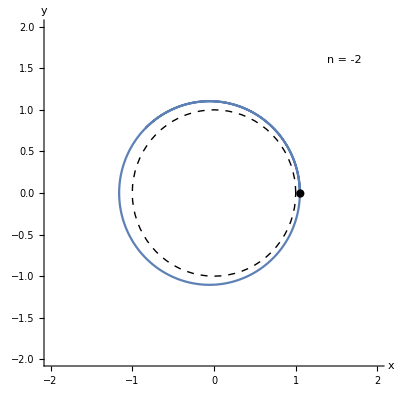

```mathematica
genPic[-2, 1, 10, {1.00,0}, {0,1},2.,2,True]
```

```mathematica
nL = Table[genPic[n, 1, 10, {1.00,0}, {0,0.6},2.,2,True],{n, -2.5,2.5,0.02}];
Export["a.gif",nL, "DisplayDurations"->{0.08}]
```

a.gif

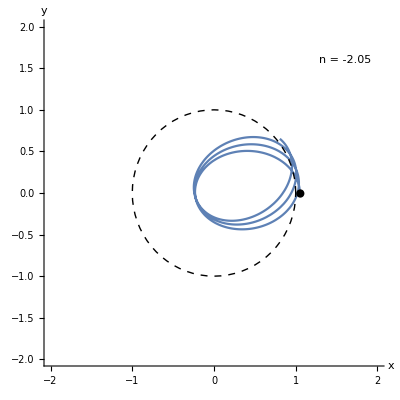

```mathematica
genPic[-2.05, 1, 10, {1.00,0}, {0,0.6},2.,2,True]
```

```mathematica
vL = Table[genPic[-2.05, 1, 30, {1.00,0}, {0,v},2.,2,True],{v,0.1, 1.1, 0.02}];
Export["vvar.gif",vL, "DisplayDurations"->{0.12}];
```

```mathematica
genPic = Function[{n, k, t1, X0, V0, range, rate, unitCircleQ},
Module
[
{t,r,F,eq,sol,path,x, trun = 0},

r=Sqrt@Sum[x[i][t]^2,{i,1,dim}];
F[r_]:=k r^n;

eq={Flatten@{
Table [-F[r] x[i][t]/r==x[i]''[t],{i,1,dim}],
{x[1][0]==X0[[1]],x[2][0]==X0[[2]]},
{x[1]'[0]==V0[[1]],x[2]'[0]==V0[[2]]}}};
sol=NDSolve[eq,Table[x[i],{i,1,dim}],{t,0,t1},MaxSteps->∞][[1]];
path=ParametricPlot[Evaluate[Table[x[i][t],{i,1,dim}]/.sol],{t,0,t1}];
(*With
[
{x1=x[1][trun]/.sol,x2=x[2][trun]/.sol},*)
Graphics[
{
path[[1]],(*!*)
Disk[{x[1][trun]/.sol,x[2][trun]/.sol},0.05],
Evaluate@If[unitCircleQ,{Dashed,Circle[{0,0},1]}],
Text["n = "~StringJoin~ToString[n],{0.8 range, 0.8 range}]
},
PlotRange->{{-range,range},{-range,range}},
Axes->True,
AxesLabel->{"x", "y"}
]
]
];
```

```mathematica
ans = Table[genPic[n, 1, 30, {1.05,0}, {0,0.6},2.,2,True], {n,{-2,-2.05,-1,1,2}}];
Table[
Export["cls"~StringJoin~ToString[i]~StringJoin~".png",ans[[i]]],
{i,1,Length[ans]}]
```

{cls1.png,cls2.png,cls3.png,cls4.png,cls5.png}

```mathematica
For[i = 1,i≤Length[ans],++i,
Export["cls"~StringJoin~ToString[i]~StringJoin~".png",ans[[i]]]
]
```

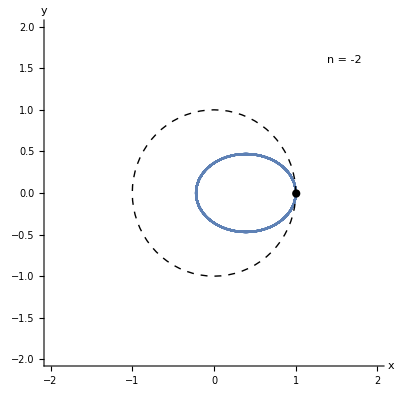
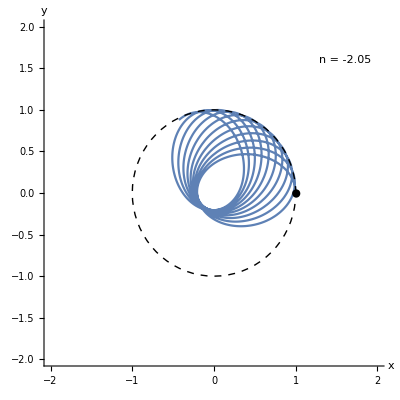
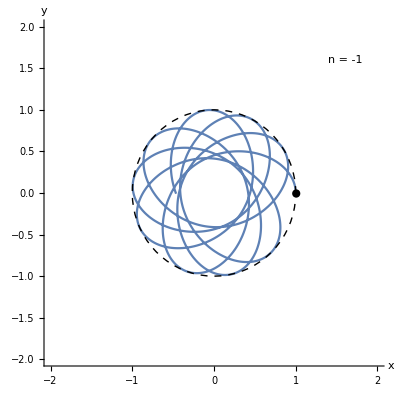
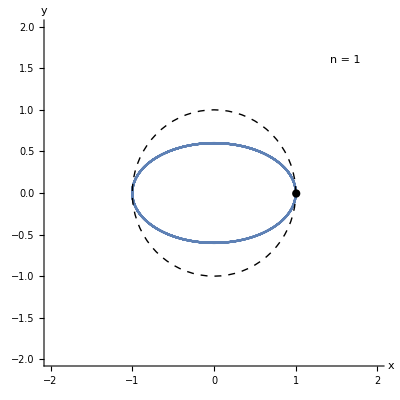
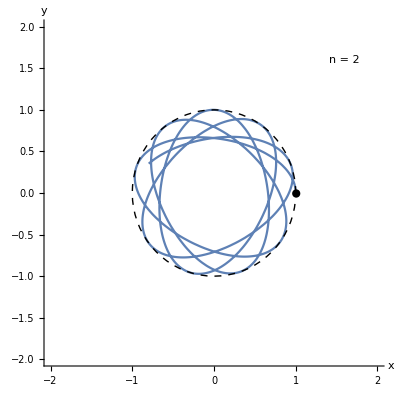

{difn1.png,difn2.png,difn3.png,difn4.png,difn5.png}

```mathematica
ans = Table[genPic[n, 1, 30, {1.00,0}, {0,0.6},2.,2,True], {n,{-2,-2.05,-1,1,2}}]
Table[
Export["difn"~StringJoin~ToString[i]~StringJoin~".png",ans[[i]]],
{i,1,Length[ans]}]
```

```mathematica
genPic = Function[{n, k, t1, X0, V0, range, rate, unitCircleQ},
Module
[
{t,r,F,eq,sol,path,x, trun = 0},

r=Sqrt@Sum[x[i][t]^2,{i,1,dim}];
F[r_]:=k r^n;

eq={Flatten@{
Table [-F[r] x[i][t]/r==x[i]''[t],{i,1,dim}],
{x[1][0]==X0[[1]],x[2][0]==X0[[2]]},
{x[1]'[0]==V0[[1]],x[2]'[0]==V0[[2]]}}};
sol=NDSolve[eq,Table[x[i],{i,1,dim}],{t,0,t1},MaxSteps->∞][[1]];
path=ParametricPlot[Evaluate[Table[x[i][t],{i,1,dim}]/.sol],{t,0,t1}];
(*With
[
{x1=x[1][trun]/.sol,x2=x[2][trun]/.sol},*)
Graphics[
{
path[[1]],(*!*)
Disk[{x[1][trun]/.sol,x[2][trun]/.sol},0.05],
Evaluate@If[unitCircleQ,{Dashed,Circle[{0,0},1]}],
Text["v = "~StringJoin~ToString[V0[[2]]],{0.8 range, 0.8 range}]
},
PlotRange->{{-range,range},{-range,range}},
Axes->True,
AxesLabel->{"x", "y"}
]
]
];
```

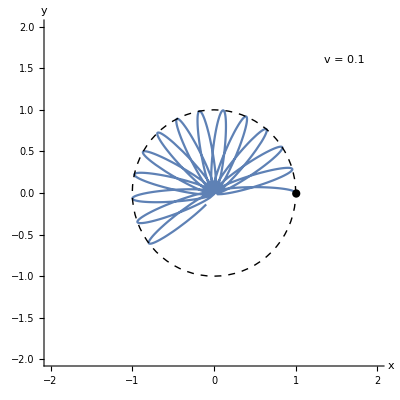
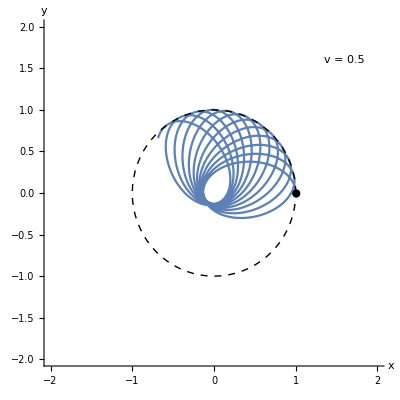
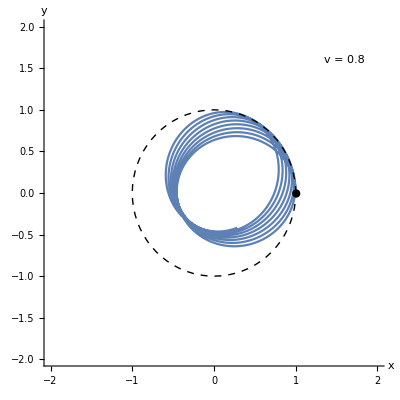
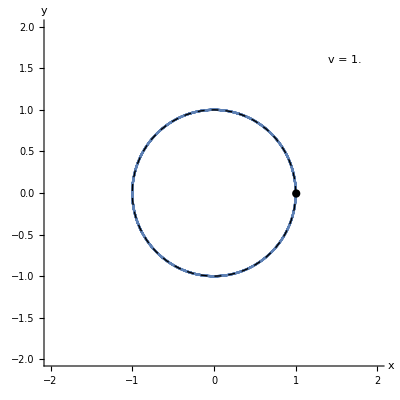

{difv1.png,difv2.png,difv3.png,difv4.png}

```mathematica
ans = Table[genPic[-2.05, 1, 30, {1.00,0}, {0,v},2.,2,True], {v,{0.1, 0.5, 0.8, 1.0}}]
Table[
Export["difv"~StringJoin~ToString[i]~StringJoin~".png",ans[[i]]],
{i,1,Length[ans]}]
```